```mathematica
(* Computer Graphics with Applications of Dr. Makhanov. (Google's Version) *)
```

```mathematica
(* Lecture 10: Loops and Modules. Introduction into 2D geometric transformations *)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot}, ImageSize->Medium,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Conditional Statements. Loops. *)
```

```mathematica
(* The "If" statement is given by If[condition, TRUE (t),FALSE (f)] gives t if condition  evaluates to Truepaclet:ref/True, and f if it evaluates to Falsepaclet:ref/False.  *)
```

```mathematica
(* Program and plot the function f(x)=sin(|x|) for {x,-5,5} using If *)
```

```mathematica
func1[x_]:=If[x<0,-x,x] (* แบบนี้เหมือนหา Abs *)
```

```mathematica
f[x_]:=Sin[func1[x]]
```

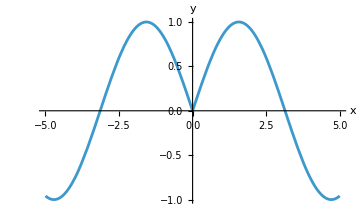

-Graphics-

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
(* Example Avoid division by zero using If *)
```

```mathematica
div1[x_,y_]:=If[y==0, "∞",x/y ] (* "∞" อันนี้เป็น String นะ ไม่ได้เป็นค่า *)
```

```mathematica
div1[1,4]
```

1/4

```mathematica
div1[2,0]
```

∞

```mathematica
(* Alternatively *)
```

```mathematica
div2[x_,y_]:=If[y!=0, x/y,"∞"]
```

```mathematica
div2[1,4]
```

1/4

```mathematica
div2[2,0]
```

∞

```mathematica
(* Plot the surface  S5[u_,v_]:= *)
```

```mathematica
S51[u_,v_]:=u^2
```

```mathematica
S52[u_,v_]:=0
```

```mathematica
S5[u_,v_]:=If[u>0,S51[u,v], S52[u,v]]
```

```mathematica
S5p[u_,v_]:={u,v,S5[u,v]}
```

```mathematica
Plot3D[S5[u,v],{u,-1,1},{v,-1,1}]
```

-Graphics3D-

```mathematica
(* There is a small problem for u=0 (empty line). This is solved as follows  *)
```

```mathematica
Plot3D[S5[u,v],{u,-1,1},{v,-1,1},Exclusions->None]
```

-Graphics3D-

```mathematica
(* Exclusions is an option that specifies where to exclude in regions used by Plot and Plot3D. 
In particular, Exclusions->None does not show what Mathematica thinks is a singularity *)
```

```mathematica
(* Design an animation of the surface S4N along S3 from L9 that changes the color in the middle of the path irrespectively of the length of the path (L/2) *)
```

```mathematica
(* We have to re-write the code from PlotPosition4[t_] *)
```

```mathematica
S3[t_]:={1.0 Sin[t],0.0299-0.0407t+0.75773 Cos[1.2 t]+0.62254Sin[t],t}
```

```mathematica
L3=10;
```

```mathematica
S4N[u_,v_]:={u,v,-0.2939+0.0024 u+0.0995 u^2-0.0028 u^3-0.0678 v-0.0048 u v+0.0176 u^2 v+0.364 v^2+0.0041 u v^2+0.063 v^3}
```

```mathematica
SurfacePosition4[u_,v_,t_]:=S4N[u,v]+S3[t]
```

```mathematica
PlotPosition4Color[t_,Color_]:=ParametricPlot3D[SurfacePosition4[u,v,t],{u,-1,1},{v,-1,1},PlotStyle->Color]
```

```mathematica
ShowAll4Color[t_]:=Show[{PlotPosition4Color[t,If[t<L3/2,Red,Blue]]},PlotRange->{{-1,1},{-1,1},{-1,10}},BoxRatios->1]
```

```mathematica
Manipulate[ShowAll4Color[t],{t,1,L3}] (* อันนี้แค่ไม่ได้ show curve เท่านั้นเอง*)
```

-Graphics-

-Graphics-

```mathematica
(* Testing the integer positive numbers Check is x is a positive integer number, calculate 1/(1+x), otherwise output error  *)
```

```mathematica
check1[x_]:=If[IntegerQ[x]&& NumberQ[x]&& Positive[x],1/(1+x),"error"]
```

```mathematica
check1[4]
```

1/5

```mathematica
check1[-1]
```

error

```mathematica
check1["num"] (* ส่ง input เป็น String เข้าไป*)
```

error

```mathematica
(* Testing and plotting prime numbers. Consider a matrix 10x10 of integer numbers given by *)
```

```mathematica
M=Table[i+10*(j-1),{j,10},{i,10}];
```

```mathematica
MatrixForm[M]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100)

```mathematica
M=Transpose[M]
```

{{1,11,21,31,41,51,61,71,81,91},{2,12,22,32,42,52,62,72,82,92},{3,13,23,33,43,53,63,73,83,93},{4,14,24,34,44,54,64,74,84,94},{5,15,25,35,45,55,65,75,85,95},{6,16,26,36,46,56,66,76,86,96},{7,17,27,37,47,57,67,77,87,97},{8,18,28,38,48,58,68,78,88,98},{9,19,29,39,49,59,69,79,89,99},{10,20,30,40,50,60,70,80,90,100}}

```mathematica
MatrixForm[M]
```

(1 | 11 | 21 | 31 | 41 | 51 | 61 | 71 | 81 | 91
2 | 12 | 22 | 32 | 42 | 52 | 62 | 72 | 82 | 92
3 | 13 | 23 | 33 | 43 | 53 | 63 | 73 | 83 | 93
4 | 14 | 24 | 34 | 44 | 54 | 64 | 74 | 84 | 94
5 | 15 | 25 | 35 | 45 | 55 | 65 | 75 | 85 | 95
6 | 16 | 26 | 36 | 46 | 56 | 66 | 76 | 86 | 96
7 | 17 | 27 | 37 | 47 | 57 | 67 | 77 | 87 | 97
8 | 18 | 28 | 38 | 48 | 58 | 68 | 78 | 88 | 98
9 | 19 | 29 | 39 | 49 | 59 | 69 | 79 | 89 | 99
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100)

```mathematica
(* Recall Graphics2D Disk[{x,y},R]  *)
```

```mathematica
R=1;
```

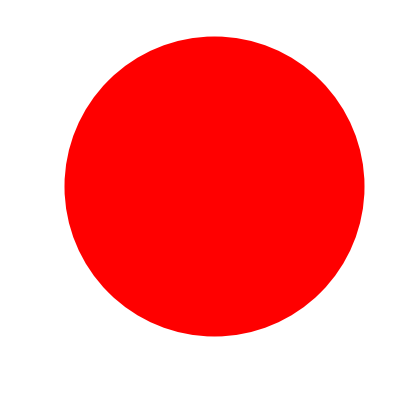

```mathematica
Graphics[{Red,Disk[{5,5},2]},ImageSize->Tiny]
```

```mathematica
(* Plot prime numbers in the numerical matric 10x10  by red circles using function PrimeQ *)
```

```mathematica
DiskC05[i_,j_,Color_]:={Color,Disk[{i,j},0.5]}
```

```mathematica
PrimeM=Table[If [PrimeQ[M[[i]][[j]]], DiskC05[i,j,Red],DiskC05[i,j,Green]],{i,10},{j,10}];
```

```mathematica
(* Plot the numbers inside the disks using Inset[insert,{x,y}].   *)
```

```mathematica
(* Example of Inset *)
```

```mathematica
x=15;
```

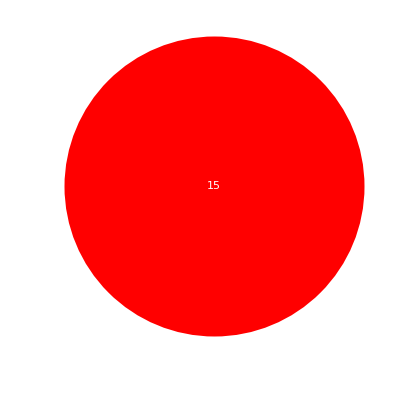

```mathematica
Graphics[Style[{Red,Disk[],White,Inset[x,{0,0}]},FontSize->45],ImageSize->Tiny]
```

```mathematica
(* Let us depict the prime numbers as follows // NOT A PART OF FINAL EXAM *)
```

```mathematica
PrimeMN=Table[If [PrimeQ[M[[i]][[j]]], {Red,Disk[{i,10-j},0.5],White,Inset[M[[i]][[j]],{i,10-j}]},{Green,Disk[{i,10-j},0.5], Blue,Inset[M[[i]][[j]],{i,10-j}]}],{i,10},{j,10}];
```

```mathematica
MatrixForm[PrimeMN];
```

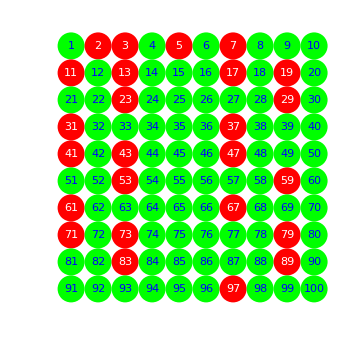

```mathematica
Graphics[Style[PrimeMN,FontSize->12]]
```

```mathematica
(* Show an interesting pattern of prime numbers for 50x50 *)
```

```mathematica
(* M1 is a matrix 50x50 M1=1,...2500. Show an interesting pattern of prime numbers for 50x50 *)
```

```mathematica
M1=Table[i+50*(j-1),{j,50},{i,50}];
```

```mathematica
M1=Transpose[M1];
```

```mathematica
PrimeM1=Table[If [PrimeQ[M1[[i]][[j]]], {Red,Disk[{i,50-j},0.5]},{Green,Disk[{i,50-j},0.5]}],{i,50},{j,50}];
```

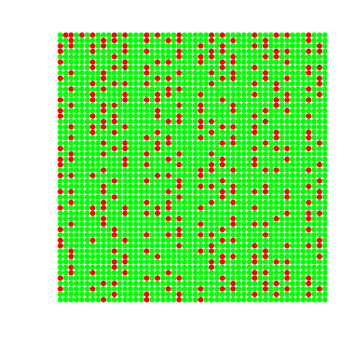

-Graphics-

```mathematica
Graphics[PrimeM1]
```

```mathematica
(* A comma delimits the parts of For, whereas the semicolon delimits the parts inside the loop *)
```

```mathematica
For[i=0,i<4,i++,Print[i]]
```

0

1

2

3

```mathematica
(*Example 2 *)
```

```mathematica
(* Find whether N1 is a prime number and output the divisor. Note the function Mod[x,y]  *)
```

```mathematica
N1=37*47;
```

```mathematica
For[i=2,i<=N1-1,i++,{If[Mod[N1,i]==0,{Print[i],Break[]}]}]
```

37

```mathematica
(* Let  us improve it by stating whether N1 is a prime *)
```

```mathematica
For[i=2,i<=N1-1,i++,{If[Mod[N1,i]==0,{Print["Divisible by ",i],Break[]},If[i==N1-1,{Print[N1," prime"]}]]}]
```

Divisible by 37

```mathematica
(* Double loop *)
```

```mathematica
(* Define the 3D spiral with the parametric length. L=25 and the radius 5. Plot the NS spheres of the radius 
RS=3 on the spiral using the For-loop. The set of the spheres must be precomputed and represented by a list *)
```

```mathematica
(* Define the 3D spiral   *)
```

```mathematica
R=5
```

5

```mathematica
L=25
```

25

```mathematica
{xS[s_]:=R Cos[s],yS[s_]:=R Sin[s],zS[s_]:=s};
```

```mathematica
Sp[t_]:={xS[t],yS[t],zS[t]}
```

```mathematica
mySpiral=ParametricPlot3D[Sp[t],{t,0,L},PlotStyle->{Red, Thickness[0.03]}]
```

-Graphics3D-

```mathematica
(* Let NS=10. Calculate the step   *)
```

```mathematica
NS=50
```

50

```mathematica
stepS=L/NS
```

1/2

```mathematica
RS=3
```

3

```mathematica
(* The first sphere *)
```

```mathematica
SList={Sphere[Sp[0],RS]}
```

{Sphere[{5,0,0},3]}

```mathematica
Graphics3D[SList,PlotRange->{{-2R,2R},{-2R,2R},{-L/5,L+R}},ImageSize->Small]
```

-Graphics3D-

```mathematica
(* Calculate the list of the spheres *)
```

```mathematica
For[i=2;SList={Sphere[Sp[0],RS]},i<=NS,i++,SList=Insert[SList,Sphere[Sp[1.0stepS*i],RS],1]];
```

```mathematica
SList;
```

```mathematica
mySpheres=Graphics3D[{Opacity[0.5],SList}]
```

-Graphics3D-

```mathematica
Show[mySpheres,mySpiral]
```

-Graphics3D-

```mathematica
(* Graphic function applies to a pre-calculated list of the spheres with a variable color  *)
```

```mathematica
Show1Sphere[Color_,i_]:=Graphics3D[{Color,SList[[i]]},PlotRange->{{-2R,2R},{-2R,2R},{-L/5,L+R}}]
```

```mathematica
Show1Sphere[Red,5]
```

-Graphics3D-

```mathematica
myShow1[Color_,i_]:=Show[mySpheres,mySpiral,Show1Sphere[Color,i]]
```

```mathematica
ColorList=RandomColor[NS]
```

{RGBColor[0.776791929922412, 0.0053281064017136615, 0.1695018071222909],RGBColor[0.5650225301100511, 0.7203874631988461, 0.11271703843720626],RGBColor[0.22939898569018702, 0.7187539579010875, 0.0064031932872483655],RGBColor[0.09349718666225315, 0.4074058863117136, 0.6885057116804716],RGBColor[0.4258898085329539, 0.8173678043076456, 0.8613500569176282],RGBColor[0.29837734715166575, 0.9119745284237113, 0.6300121198346218],RGBColor[0.6597210272919456, 0.5006322440072319, 0.45852463948333866],RGBColor[0.6628675104013302, 0.5621307931329682, 0.6292063693103036],RGBColor[0.038921095920894544, 0.364603802513376, 0.20851486286601406],RGBColor[0.6499151849293634, 0.3534876241098681, 0.47549677017644476],RGBColor[0.1456345760043125, 0.3871288075517658, 0.3215865813390959],RGBColor[0.10490905734282507, 0.32362872049904645, 0.6125718086213985],RGBColor[0.6416920525879914, 0.8077857001651949, 0.9839191311671873],RGBColor[0.7558240027624612, 0.3324303855592199, 0.614569666857713],RGBColor[0.17990319467130478, 0.26635364930194627, 0.03266354836202634],RGBColor[0.3945104296495878, 0.5418672523474022, 0.6014910893956869],RGBColor[0.2036279144903761, 0.5525696896924526, 0.5129389881848303],RGBColor[0.35501955607215185, 0.5082237098888955, 0.589477135548897],RGBColor[0.7263127548036066, 0.7319506678915679, 0.6834093452143408],RGBColor[0.8955689810926291, 0.5575475194084616, 0.24315611807348336],RGBColor[0.34935965594217455, 0.6276871327181239, 0.06619261521017017],RGBColor[0.6645218304909346, 0.8403591960515335, 0.7852447656531987],RGBColor[0.63246918213438, 0.6065642401198015, 0.26151882489066747],RGBColor[0.7633556407734252, 0.4712490023827929, 0.7987864039986048],RGBColor[0.8194264214125886, 0.9926434274272724, 0.8035009834612878],RGBColor[0.6573818421697966, 0.1434075752173085, 0.4546875141407183],RGBColor[0.06899541463466052, 0.7757829512736942, 0.789858511090582],RGBColor[0.5438535084506644, 0.8097800478939823, 0.819060337907086],RGBColor[0.7283543022779415, 0.7593202964799739, 0.4502840678385083],RGBColor[0.5588624696724542, 0.2911646985861045, 0.11146939596380534],RGBColor[0.4481801695523411, 0.9129744883938391, 0.35712048583316847],RGBColor[0.6055734362480842, 0.8251013719549718, 0.006639413783876558],RGBColor[0.3347002877996401, 0.6138995601830952, 0.06860012009775973],RGBColor[0.1685200383729859, 0.5098578190542735, 0.5247202918584464],RGBColor[0.4771519514349516, 0.6055718215676429, 0.8142215954383691],RGBColor[0.9149662166583852, 0.2549871874234029, 0.6185309248994248],RGBColor[0.09346873793128974, 0.3749757045954769, 0.9433340889194282],RGBColor[0.04445500444271433, 0.4610215362197596, 0.983785841821065],RGBColor[0.7916470471893842, 0.3422318648283851, 0.5251626088591781],RGBColor[0.4671281535469256, 0.028796847874825726, 0.43680763428806824],RGBColor[0.6737828245832949, 0.7010260896228384, 0.6906934060778542],RGBColor[0.7952979052870965, 0.7476571033446471, 0.12095074753008861],RGBColor[0.9552244855772765, 0.7460351196682493, 0.6709296365113977],RGBColor[0.24911503141356306, 0.5703319029668104, 0.4924988555195702],RGBColor[0.004182507322244788, 0.2520042284463675, 0.0064336672364671],RGBColor[0.3245781333824509, 0.5382752740299477, 0.7508663677937428],RGBColor[0.8552094528623106, 0.7028272831960858, 0.7034866888809013],RGBColor[0.04327786444677817, 0.1096702012312385, 0.24053966917334013],RGBColor[0.004030412557499252, 0.6214611416842046, 0.711043163013626],RGBColor[0.5606248974550079, 0.05106089360268662, 0.5346196555573335]}

```mathematica
Manipulate[myShow1[Color,i],{i,1,NS,1},{Color,ColorList}]
```

```mathematica
(* Find the sum of integers from 1 to N using module and the For - loop    *)
```

```mathematica
f2[N_]:=Module[{sum=0},For [i=1,i<=N,i++, sum+=i;];sum]
```

```mathematica
f2[15]
```

120

```mathematica
(* Find whether N is a prime number using the function Mod  *)
```

```mathematica
fp[N_]:=Module[{flag="prime"},For[i=2,i<=N-1,i++,{If[Mod[N,i]==0,{flag="not prime",Break[]}]}];flag]
```

```mathematica
fp[37]
```

prime

```mathematica
N1=37*22
```

814

```mathematica
fp[N1]
```

not prime

```mathematica
(* Change fp to True/False and  create a list of prime numbers in the range from 0 to N and display them as the ListPlot*)
```

```mathematica
fp2[N_]:=Module[{flag=True,i},For[i=2,i<=N-1,i++,{If[Mod[N,i]==0,{flag=False ,Break[]}]}];flag]
```

```mathematica
fp2[37]
```

True

```mathematica
(* Remark. Compare the use of Table  *)
```

```mathematica
LpT[N1_]:=Module[{L},L=Table [If[fp2[i],i],{i,N1}];L]
```

```mathematica
LpT[37]
```

{1,2,3,Null,5,Null,7,Null,Null,Null,11,Null,13,Null,Null,Null,17,Null,19,Null,Null,Null,23,Null,Null,Null,Null,Null,29,Null,31,Null,Null,Null,Null,Null,37}

```mathematica
(* The Nulls can be fixed as follows *)
```

```mathematica
LpTF[N1_]:=Module[{L},L=Table [If[fp2[i],i, Nothing],{i,N1}];{L,ListPlot[L,PlotStyle->{Blue,PointSize->0.04},DataRange->37]}] (* ทีแรกไม่มี plot เพิ่มมา *)
```

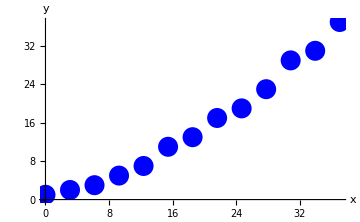
{{1,2,3,5,7,11,13,17,19,23,29,31,37},-Graphics-}

```mathematica
GN=LpTF[37]
```

```mathematica
(* Plot the result *)
```

```mathematica
ListPlot[GN,PlotStyle->{Blue,PointSize->0.04},DataRange->37]
```

-Graphics-

```mathematica
(* Collecting objects in the lists. 
Consider a 2D spiral PolarPlot[t,{t,0,a}]. Write a module to plot and collect the spirals for {a,10,20} with N values  *)
```

```mathematica
amax=20;
```

```mathematica
Ra=1;
```

```mathematica
G[a_]:=PolarPlot[t,{t,0,a},PlotRange->amax]
```

```mathematica
G[20];
```

```mathematica
SpiralCollection[N_,a1_,a2_]:=Module[{step,PL,a},step=(a2-a1)/(N-1); PL=Table[G[a],{a,a1,a2,step}];PL]
```

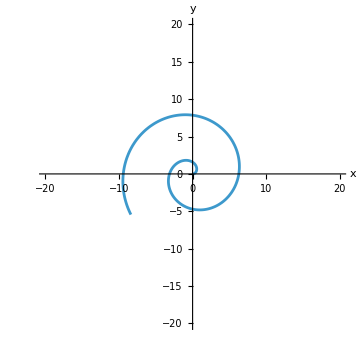
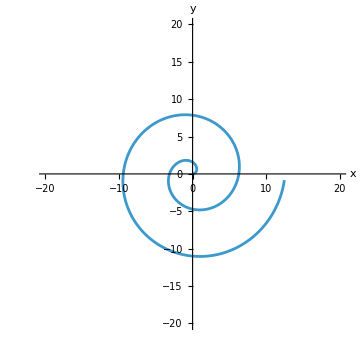
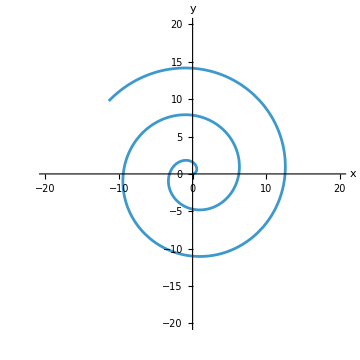
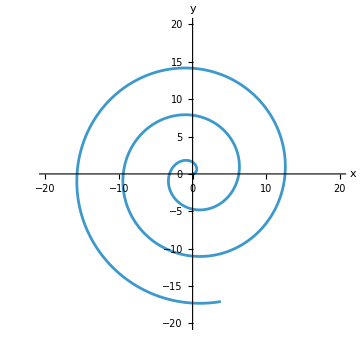
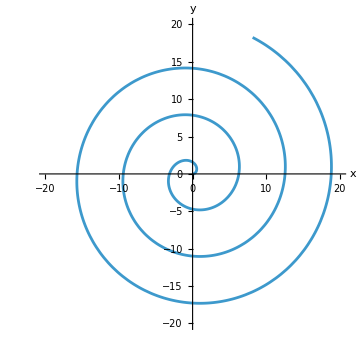

```mathematica
SC=SpiralCollection[5,10,20]
```

```mathematica
ListAnimate[SC,AnimationRunning->False]
```

```mathematica
(* Geometric transformations *)
```

```mathematica
(* In the world of primitives rotations and translations are performed by functions GeometricTransformation,
RotationTransform[angle] (around the origin).TranslationTransform[Point]and Composition. 
The extended version is RotationTransform[angle,pointaround] *)
```

```mathematica
(* Example 1. Translations *)
```

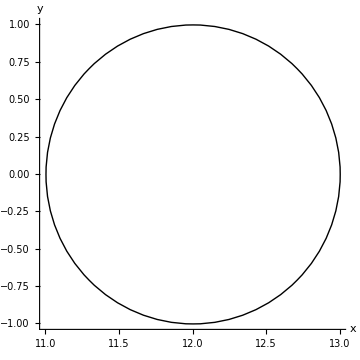

```mathematica
Graphics[{GeometricTransformation[Circle[],TranslationTransform[{12,0}]]}, Axes->True]
```

```mathematica
(* Superposition of the Transformations  *)
```

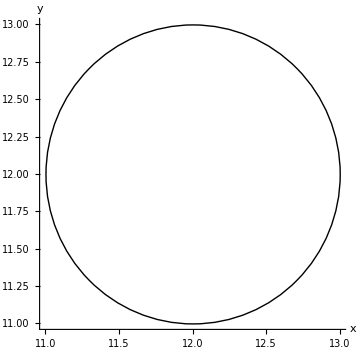

```mathematica
Graphics[{GeometricTransformation[Circle[],Composition[TranslationTransform[{12,0}],TranslationTransform[{0,12}]]]}, Axes->True]
```

```mathematica
(* Multiple transforms applied to 1 object   *)
```

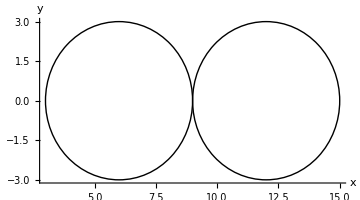

```mathematica
Graphics[{GeometricTransformation[Circle[{0,0},3],{TranslationTransform[{6,0}],TranslationTransform[{12,0}]}]}, Axes->True]
```

```mathematica
(* Example 2 Rotations. Rotate the equilateral (regular) triangle around the origin *)
```

```mathematica
(* Set the equilateral )(regular) triangle, RT=1, using the RegularPolygon *)
```

```mathematica
RT=1;CTri={0,0};
```

```mathematica
PTri={Red,RegularPolygon[CTri,RT,3]}
```

{RGBColor[1, 0, 0],RegularPolygon[{0,0},1,3]}

```mathematica
T[a_]:=Graphics[{GeometricTransformation[PTri,RotationTransform[a]]},Axes->True,PlotRange->3]
```

```mathematica
Manipulate[T[t],{t,0,2Pi,0.1}]
```

```mathematica
(* Example 3 Rotate an equilateral triangle RT=2 at the RR=7/2 from the origin. At the same time rotate the triangle around itself.*)
```

```mathematica
RT=1;
```

```mathematica
(* Triangle at the position PTriNew=CirclePoints[2,3]+{7/2,0} *)
```

```mathematica
(* Check every step! *)
```

```mathematica
RR={7/2,0};
```

```mathematica
(* Center *)
```

```mathematica
CTri={0,0};
```

```mathematica
(* Shift the x coordinate by RR *)
```

```mathematica
ObjectTri=RegularPolygon[CTri,RT,3]
```

RegularPolygon[{0,0},1,3]

```mathematica
(* The Triangle and the anchor point *)
```

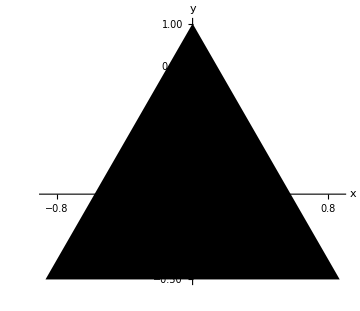

```mathematica
Graphics[ObjectTri,Axes->True,AxesOrigin->{0,0},PlotRange->1.5]
```

```mathematica
(* Compose the rotation function and apply to both the object and the center point is CTri. The composed transformation is generated by Composition  *)
```

```mathematica
TTri[a_]:=GeometricTransformation[ObjectTri,Composition[RotationTransform[a],TranslationTransform[RR]]]
```

```mathematica
(* Display graphics function  *)
```

```mathematica
FTriT[a_]:=Graphics[TTri[a],Axes->True, AxesOrigin->{0,0},PlotRange->4.5]
```

```mathematica
Manipulate[FTriT[t],{t,0,2Pi-0.01,0.1}]
```

```mathematica
(* Additionally rotate the object around itself *)
```

```mathematica
TriRR[a_]:=GeometricTransformation[ObjectTri,Composition[RotationTransform[a],TranslationTransform[RR],RotationTransform[a]]]
```

```mathematica
FTriRR[a_]:=Graphics[TriRR[a],Axes->True, AxesOrigin->{0,0},PlotRange->5.5]
```

```mathematica
Manipulate[FTriRR[t],{t,0,2Pi-0.0001,0.1}]
```

```mathematica
(* Instead of rotation around the origin translate along the curve {Cos[3t],Sin[2t] *)
```

```mathematica
Curve6[t_]:={2 Cos[3t],2Sin[2t]}
```

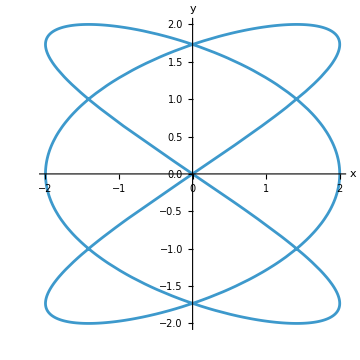

```mathematica
PC6=ParametricPlot[Curve6[t],{t,0,2Pi}]
```

```mathematica
TriCurve6[a_,t_]:=GeometricTransformation[ObjectTri,Composition[TranslationTransform[Curve6[t]],RotationTransform[a]]]
```

```mathematica
FTri6[a_,t_]:=Graphics[TriCurve6[a,t],Axes->True, AxesOrigin->{0,0},PlotRange->3]
```

```mathematica
ShowAll6[a_,t_]:=Show[FTri6[a,t],PC6]
```

```mathematica
(* the rotation speed *)
```

```mathematica
a=10;
```

```mathematica
Manipulate[ShowAll6[a t,t],{t,0,2Pi-0.0001,0.1}]
```